```mathematica
dir=NotebookDirectory[];
files=FileNames["Angles45deg_*.csv",dir];
```

```mathematica
process[file_]:=Module[{data,headers,tcol,acol,time,angle},data=Import[file,"CSV"];
headers=First[data];
tcol=First@FirstPosition[headers,"Time"];
acol=First@FirstPosition[headers,"Angle"];
time=4data[[All,tcol]];
angle=-data[[All,acol]];
Transpose@{Rest[time],(Rest[angle]-angle[[2]])*Pi/180}];
```

```mathematica
results = AssociationMap[process, files];
```

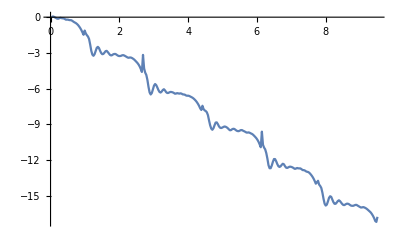
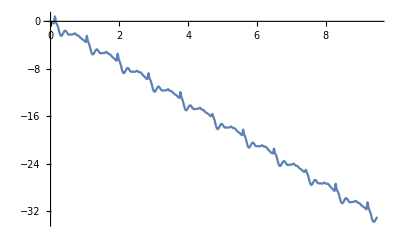
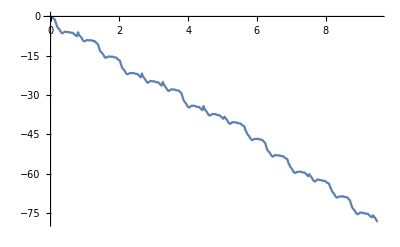
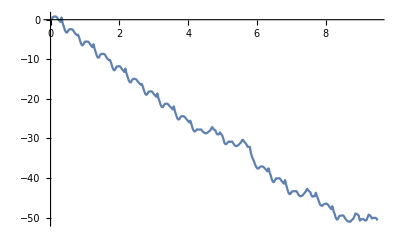
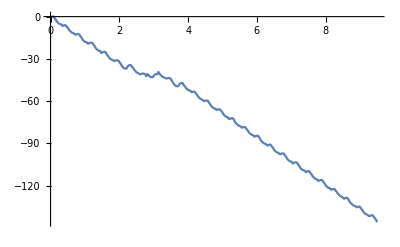
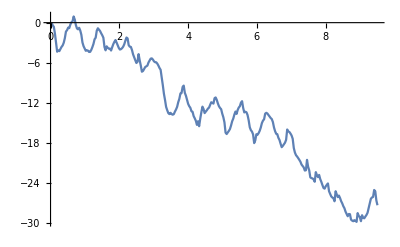

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}]
```

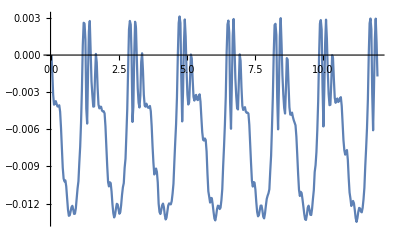
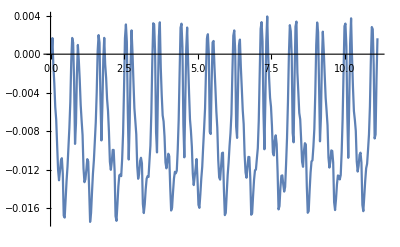
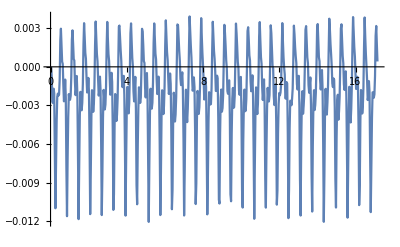
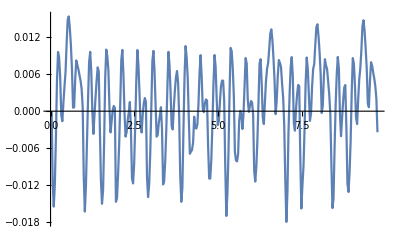
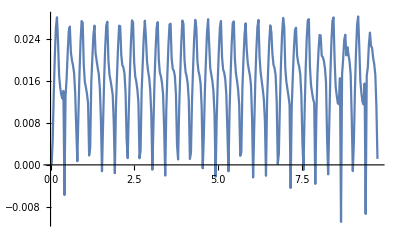
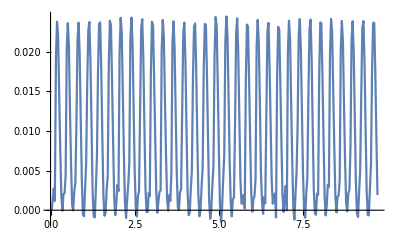

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_5cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*These feel more like flappings*)
```

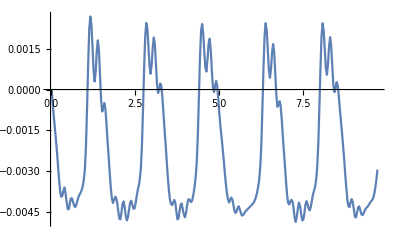
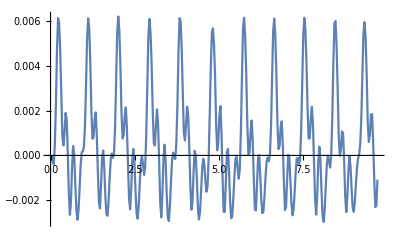
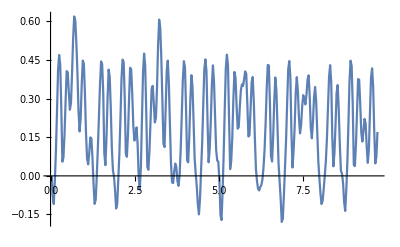
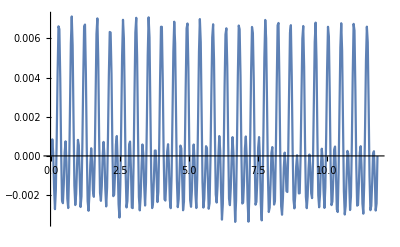
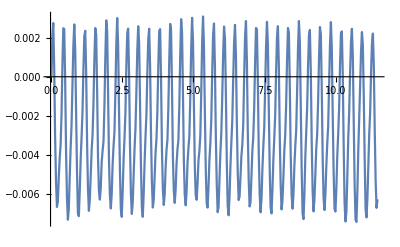
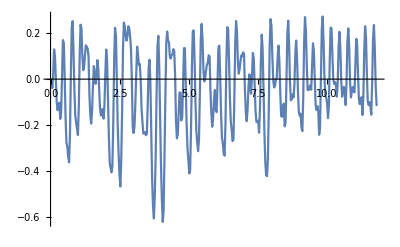

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_6cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*i = 3, 6 seem to be doing more than just small oscillations in movies*)
```

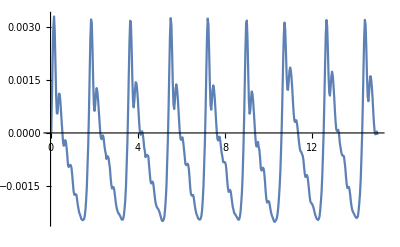
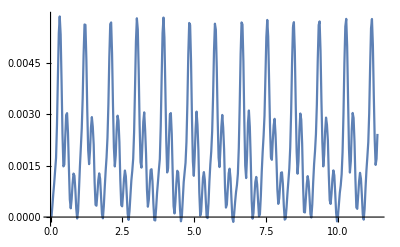
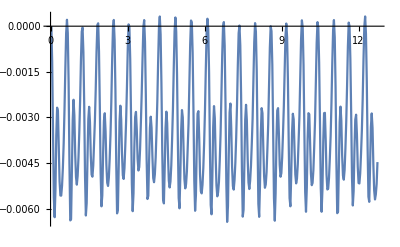
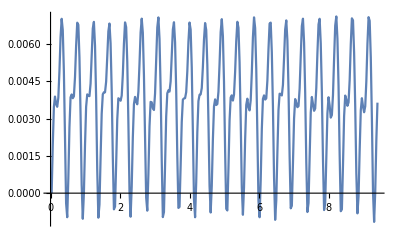
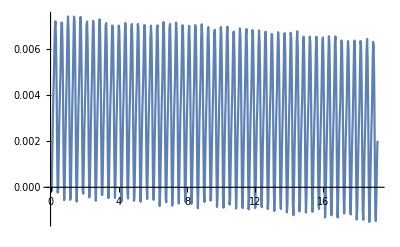
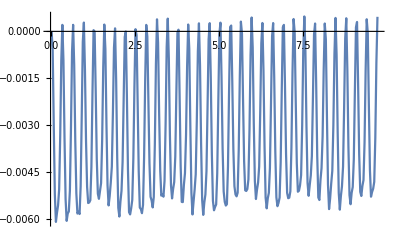

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_7cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}]
```

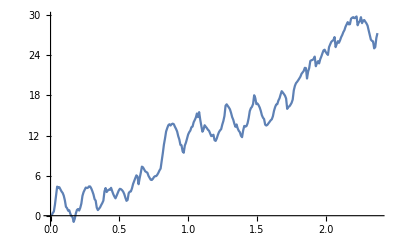
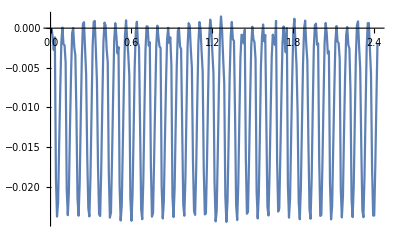
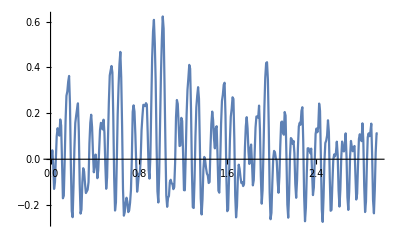
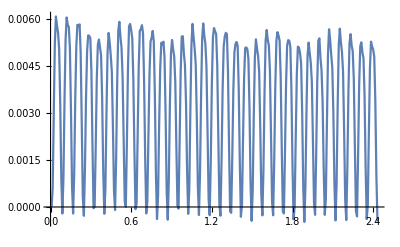

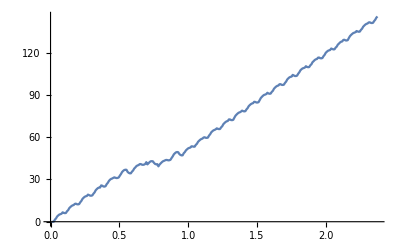
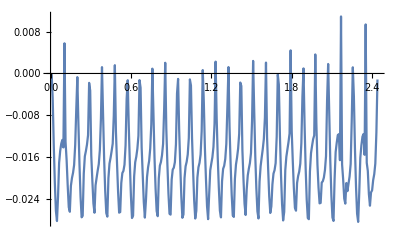
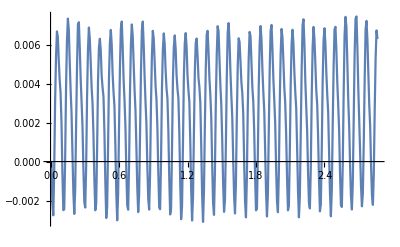
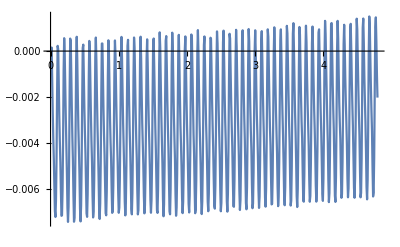

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_"<>ToString[i] <> "cm_6hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_"<>ToString[i] <> "cm_5hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_"<>ToString[i] <> "cm_4hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_"<>ToString[i] <> "cm_3hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_"<>ToString[i] <> "cm_2hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_"<>ToString[i] <> "cm_1hz.csv"]], {i, 4,7}]
```

## Spinning modes/Harmonic resonances

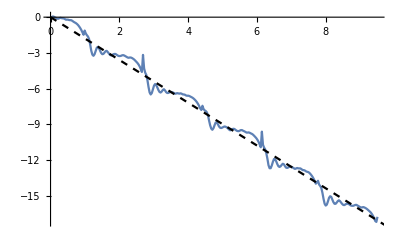

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_1hz.csv"]],
Plot[{-2Pi x (1/2)4/7}, {x, 0, 12}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

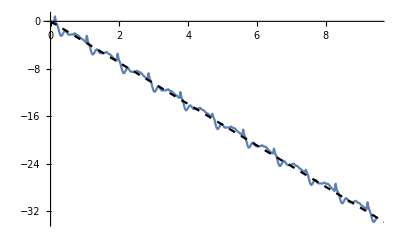

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_2hz.csv"]],
Plot[{-2Pi x (2/2)5/9}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

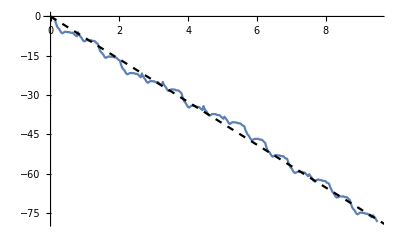

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_3hz.csv"]],
Plot[{-2Pi x (3/2)13/15}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

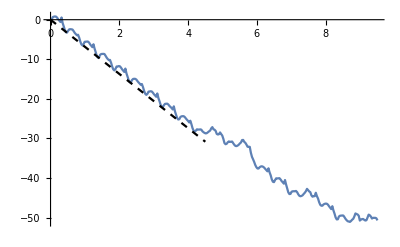

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_4hz.csv"]],
Plot[{-2Pi x (4/2)6/11}, {x, 0, 4.5}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

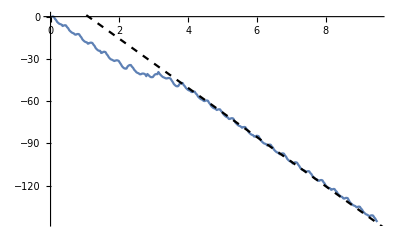

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_5hz.csv"]],
Plot[{ -2Pi (x-1.1) (5/2)10/9}, {x, 0, 14}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```

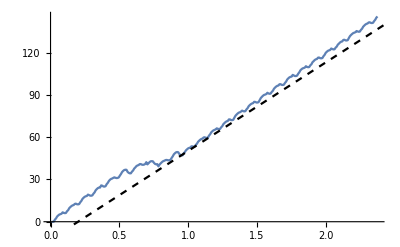

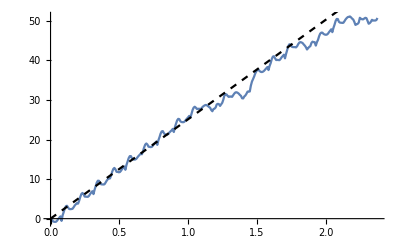

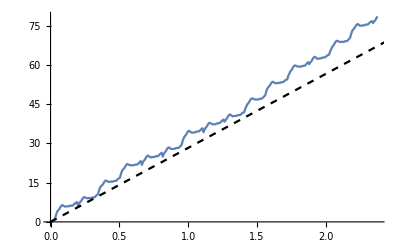

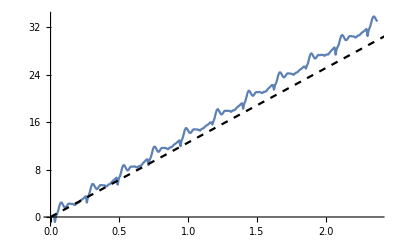

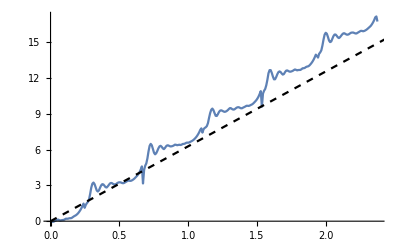

```mathematica
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_5hz.csv"]],
Plot[{ 2Pi (x-0.2) (5/2)4}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_4hz.csv"]],
Plot[{2Pi x (4/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_3hz.csv"]],
Plot[{2Pi x (3/2)3}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_2hz.csv"]],
Plot[{2Pi x (2/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
Show[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_45deg\\Angles45deg_4cm_1hz.csv"]],
Plot[{2Pi x (1/2)2}, {x, 0, 4}, PlotStyle->{{Dashed,Black},{ Dashed, Purple}}]]
```